```mathematica
ResourceFunction["MaTeXInstall"][]
```

## Q 1 Q2 integrated profiles vs t

```mathematica
<<MaTeX`
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/Q2_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=10timestep;
TimeSlice2=25/timestep;
TimeSlice3=60/timestep;

radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
```

```mathematica
(*RUN this part also*)
Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=Qexpectation[n,2,time];
FIG=ListPlot[{
Table[ {TimeSlice, Sum[Obs[n,TimeSlice/timestep],{n,xmin,xmax}]
} ,{TimeSlice,0,timestep TimeSlice3,timestep}]
(*,Avalanche*)
(*,Table[
{TimeSlice, Sum[Obs2[n,TimeSlice],{n,xmin,xmax}]} ,{TimeSlice,0, TimeSlice3,1}]*)
},
Joined->False
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"t","\\sum_x \\mathcal{Q}^{\\pm}_{x}(t)"},FontSize->16]
,LabelStyle->Directive[FontSize->12]
,LABELS={
"t="<>ToString[TimeSlice3*timestep]
,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"
};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 12],{1.0,0.6}]
,PlotRange->{{0,TimeSlice3 timestep},{Automatic,Automatic}}
,PlotMarkers->{
{BLUE0,radius},
{RED0, radius}
}
 ]
```

-Graphics-

## Q 1 Q2 averaged profiles

```mathematica
<<MaTeX`
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/Q1_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)

radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
```

```mathematica
(*RUN this part also*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=10/timestep;
TimeSlice2=25/timestep;
TimeSlice3=60/timestep;


Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=time^1Qexpectation[n,3,time];

AvrgData={};
AverWindow =3;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
(*If[Abs[obs]>10^-6,*)
average +=obs;
counter++;
;

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}]

FIG=ListPlot[{
Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+0,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+1,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+2,xmax,3}]
(*,Table[{(A[[n+SystemSize*Floor[TimeSlice1],1]]+SHIFT)/(TimeSlice1*timestep),Obs[n,TimeSlice1]},{n,xmin,xmax}]*)
(*,AvrgData*)
(*,{0} *)(*This is technical thing to match plot frame boxes with other plots
I add it to use legenda sigma^x ...
*)
},
Joined->True
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\ell/t","t\\mathcal{Q^-}_1(\\ell/t)"},FontSize->16]
,LabelStyle->Directive[FontSize->12]
,LABELS={
"0mod3; t="<>ToString[TimeSlice3*timestep]
(*,"Avrg Over "<>ToString[AverWindow]<>"Sites"*)
(*,"t="<>ToString[TimeSlice2*timestep]*)
,"1mod3; t="<>ToString[TimeSlice3*timestep]
,"2mod3; t="<>ToString[TimeSlice3*timestep]
(*,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"*)

};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 12],{1.0,0.6}]
,PlotRange->{{-7,7},{-12,12}}
,PlotMarkers->{
{BLUE0,radius},
{RED0, radius},
{GREEN0, radius}
}
 ]
```

-Graphics-

```mathematica
Averaging[window_,{
AvrgData={};
AverWindow =window;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
If[Abs[obs]>10^-6,
{average +=obs;
counter++;
}];

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}];
Return AvrgData;
}]
```

Averaging[window_,{Null}]

## {(S^z)_(3l+a)(t)} UUD profile

```mathematica
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/SxSySz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[σ^x, l], (σ^y)_(l,)Subscript[σ^z, l]*)
(*A=Cases[A,_?(Mod[#[[1]],2]==0&)];*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize;
timestep=0.1;
<<MaTeX`;
TimeSlice1 = 10/timestep;
TimeSlice2 = 60/timestep;
SHIFT=1;
(*technical part:  point types etc *)
radius=10;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];


RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];

everypoint=3;

P[l_,time_,col_]:=A[[l+SystemSize*Floor[time],col]];
Obs[l_,time_]:=  P[l,time,2];
FIG=ListPlot[{
  (*  Table[{(P[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), 2P[l,TimeSlice1,4]},{l,xmin,xmax,everypoint}]*)
Table[{(P[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), 2P[l,TimeSlice2,4]},{l,xmin,xmax,everypoint}]

(* ,Table[{(P[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), 2P[l,TimeSlice1,4]},{l,xmin+1,xmax,everypoint}]*),Table[{(P[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), 2P[l,TimeSlice2,4]},{l,xmin+1,xmax,everypoint}]

(*,Table[{(P[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), 2P[l,TimeSlice1,4]},{l,xmin+2,xmax,everypoint}]*),Table[{(P[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), 2P[l,TimeSlice2,4]},{l,xmin+2,xmax,everypoint}]

},
PlotRange->{{-10.5,10.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->False,
Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\ell/t","\\sigma^z_{\\ell}"},FontSize->16],
LabelStyle->Directive[FontSize->12],
PlotLegends->{Placed[MaTeX[{
(*"\\sigma^z_{3\\ell}(t="<>ToString[TimeSlice1*timestep]<>")",*)
"\\sigma^z_{3\\ell}(t="<>ToString[TimeSlice2*timestep]<>")",

(*"\\sigma^z_{3\\ell+1}(t="<>ToString[TimeSlice1*timestep]<>")",*)
"\\sigma^z_{3\\ell+1}(t="<>ToString[TimeSlice2*timestep]<>")",

(*"\\sigma^z_{3\\ell+2}(t="<>ToString[TimeSlice1*timestep]<>")",*)
"\\sigma^z_{3\\ell+2}(t="<>ToString[TimeSlice2*timestep]<>")"


},FontSize->12],{1.,0.6}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
{GREEN0,radius}
,{BLUE0,radius}
,{RED0, radius}
(*,{BLUE,radius}*)

(*,{BLUE0,radius}*)
(*,{RED1,radius}*)

(*,{BLACK,0.008},{BLACK,0.008}*)
}

 ]
```

-Graphics-

## S^vN profiles

```mathematica
<<MaTeX`
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/Entropy_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)

radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
```

```mathematica
(*RUN this part also*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=10/timestep;
TimeSlice2=25/timestep;
TimeSlice3=60/timestep;


Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=Qexpectation[n,2,time];

AvrgData={};
AverWindow =1;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
(*If[Abs[obs]>10^-6,*)
average +=obs;
counter++;
;

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}]

FIG=ListPlot[{
Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+0,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+1,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+2,xmax,3}]
(*,Table[{(A[[n+SystemSize*Floor[TimeSlice1],1]]+SHIFT)/(TimeSlice1*timestep),Obs[n,TimeSlice1]},{n,xmin,xmax}]*)
(*,AvrgData*)
(*,{0} *)(*This is technical thing to match plot frame boxes with other plots
I add it to use legenda sigma^x ...
*)
},
Joined->True
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\ell/t","\\mathcal{S}_{vN}(\\ell/t)"},FontSize->16]
,LabelStyle->Directive[FontSize->12]
,LABELS={
"0mod3; t="<>ToString[TimeSlice3*timestep]
(*,"Avrg Over "<>ToString[AverWindow]<>"Sites"*)
(*,"t="<>ToString[TimeSlice2*timestep]*)
,"1mod3; t="<>ToString[TimeSlice3*timestep]
,"2mod3; t="<>ToString[TimeSlice3*timestep]
(*,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"*)

};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 12],{1.0,0.6}]
,PlotRange->{{-7,7},{Automatic,Automatic}}
,PlotMarkers->{
{BLACK,radius},
{RED0, radius},
{GREEN0, radius}
}
 ]
```

-Graphics-

```mathematica
Averaging[window_,{
AvrgData={};
AverWindow =window;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
If[Abs[obs]>10^-6,
{average +=obs;
counter++;
}];

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}];
Return AvrgData;
}]
```

Averaging[window_,{Null}]

## ED

```mathematica
L=9;
SX=SparseArray[{Band[{2,1}]->0},{2,2}];
SY=SparseArray[{Band[{1,2}]->0},{2,2}];
SZ=SparseArray[{Band[{1,1}]->0},{2,2}];
un=SparseArray[{Band[{1,1}]->1},{2,2}];
SX[[1,2]]=1.;SX[[2,1]]=1;
SY[[1,2]]=-ⅈ;SY[[2,1]]=ⅈ;
SZ[[1,1]]=1;SZ[[2,2]]=-1;

Table[sz[j]=KroneckerProduct@@Join[Table[un,j-1],{SZ},Table[un,L-j]],{j,L}];
Table[sx[j]=KroneckerProduct@@Join[Table[un,j-1],{SX},Table[un,L-j]],{j,L}];
Table[sy[j]=KroneckerProduct@@Join[Table[un,j-1],{SY},Table[un,L-j]],{j,L}];
b[j_]:= 1/2(sx[j].sy[j+1].sz[j+2]-sy[j].sx[j+1] .sz[j+2]
-(sz[j-1].sx[j].sy[j+1]- sz[j-1].sy[j].sx[j+1])
);
A[j_]:= sx[j].sy[j+1]-sy[j].sx[j+1] ;
B=Sum[b[j],{j,2,L-2}];


up = {1.,0};
down = {0,1.};
left = {1./(√2),-1/(√2)};
right= {1./(√2),1./(√2)};
JIS = KroneckerProduct[up,up,up,down,down,up,down,down,down]//Flatten;
(*
JIS = KroneckerProduct[up,down]//Flatten;
JIS.A[1].JIS
*)
JIS.MatrixExp[B].JIS
```

6.3843+0. ⅈ

```mathematica
A[1].JIS//MatrixForm//Chop
```

(0
0
0.-2. ⅈ
0)

```mathematica
JIS
```

{0.,1.,0.,0.}

## XXZ large Delta

```mathematica
SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];
A=Import["UUD/N1000/Sz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
(*A=Cases[A,_?(Mod[#[[1]],2]==0&)];*)

XXZ16=Import["XXZ/Delta16/Sz_profile.dat"];
XXZ16=Drop[XXZ16,1];
XXZ16=DeleteCases[XXZ16,_?(Length[#]<4&)];
XXZ16=Chop[XXZ16[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)

XXZ8=Import["XXZ/Delta8/Sz_profile.dat"];
XXZ8=Drop[XXZ8,1];
XXZ8=DeleteCases[XXZ8,_?(Length[#]<4&)];
XXZ8=Chop[XXZ8[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)

XXZ4=Import["XXZ/Delta4/Sz_profile.dat"];
XXZ4=Drop[XXZ4,1];
XXZ4=DeleteCases[XXZ4,_?(Length[#]<4&)];
XXZ4=Chop[XXZ4[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

```mathematica
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSizeFolded =Length[Sites]; 
xminFolded=1;
xmaxFolded=SystemSizeFolded;

Sites=XXZ16[[;;,1]];
Sites=Union[Sites];
SystemSizeXXZ16 =Length[Sites]; 
xminXXZ16=1;
xmaxXXZ16=SystemSizeXXZ16;

Sites=XXZ8[[;;,1]];
Sites=Union[Sites];
SystemSizeXXZ8 =Length[Sites]; 
xminXXZ8=1;
xmaxXXZ8=SystemSizeXXZ8;

Sites=XXZ4[[;;,1]];
Sites=Union[Sites];
SystemSizeXXZ4 =Length[Sites]; 
xminXXZ4=1;
xmaxXXZ4=SystemSizeXXZ4;


timestep=0.1;

TimeSlice1 = 5/timestep;
TimeSlice2 = 5/timestep;
TimeSlice3 = 5/timestep;
TimeSlice4 = 5/timestep;
SHIFT=1;
(*technical part:  point types etc *)
radius=0.1;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
<<MaTeX`

RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];

everypoint=1;

DataFolded[l_,time_,col_]:=A[[l+SystemSizeFolded*Floor[time],col]];
ObsFolded[l_,time_]:= 2 DataFolded[l,time,2];

DataXXZ16[l_,time_,col_]:=XXZ16[[l+SystemSizeXXZ16*Floor[time],col]];
ObsXXZ16[l_,time_]:= 4DataXXZ16[l,time,3];

DataXXZ8[l_,time_,col_]:=XXZ8[[l+SystemSizeXXZ8*Floor[time],col]];
ObsXXZ8[l_,time_]:= 4DataXXZ8[l,time,3];

DataXXZ4[l_,time_,col_]:=XXZ4[[l+SystemSizeXXZ8*Floor[time],col]];
ObsXXZ4[l_,time_]:= 4DataXXZ4[l,time,3];

FIG=ListPlot[{

Table[{(DataFolded[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), ObsFolded[l,TimeSlice1]},{l,xminFolded,xmaxFolded,everypoint}]

,Table[{(DataXXZ16[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), (ObsXXZ16[l,TimeSlice2])},{l,xminXXZ16,xmaxXXZ16,everypoint}]
,Table[{(DataXXZ8[l,TimeSlice3,1]+SHIFT)/(TimeSlice3*timestep), (ObsXXZ8[l,TimeSlice3])},{l,xminXXZ8,xmaxXXZ8,everypoint}]
,Table[{(DataXXZ4[l,TimeSlice4,1]+SHIFT)/(TimeSlice4*timestep), (ObsXXZ4[l,TimeSlice4])},{l,xminXXZ4,xmaxXXZ4,everypoint}]



},
PlotRange->{{-10.5,10.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->False,
Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\ell/t","\\sigma^z_{\\ell}"},FontSize->16],
LabelStyle->Directive[FontSize->12],
PlotLegends->{Placed[MaTeX[{
"Folded\\quad \\sigma^z_{\\ell}(t="<>ToString[TimeSlice1*timestep]<>")"
,"XXZ-16\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSlice2*timestep]<>")"
,"XXZ-8\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSlice2*timestep]<>")"
,"XXZ-4\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSlice2*timestep]<>")"
},FontSize->12],{1.,0.6}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

(*,PlotMarkers->{
{RED0,radius}
,{BLUE0,radius}
,{RED0, radius}
(*,{BLUE,radius}*)

(*,{BLUE0,radius}*)
(*,{RED1,radius}*)

(*,{BLACK,0.008},{BLACK,0.008}*)
}
*)
 ]
```

-Graphics-

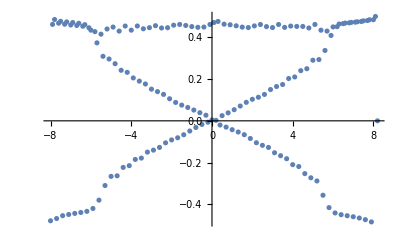

```mathematica
TimeSlice1=100;ListPlot[Table[{(P[l,TimeSlice2,1]+SHIFT)/(TimeSlice1*timestep), 2P[l,TimeSlice1,3]},{l,xmin,xmax,everypoint}]]
```

```mathematica
Limit[(1+(1/n^2))^n,n->∞]
```

1

```mathematica
ResourceFunction["MaTeXInstall"]
```

```mathematica
Needs["MaTeX`"]
```

Paclet[MaTeX,1.7.8,<>]

```mathematica
<<MaTeX`
```

## Saverio for <Sx_i Sy_(i+2)>

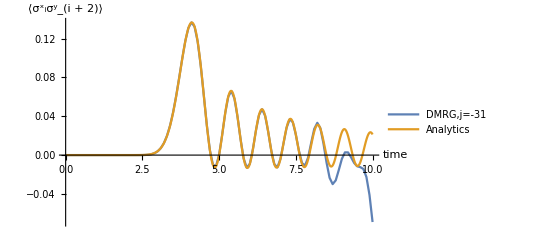

```mathematica
SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/"];
A=Import["Data/Sav/Correlation2.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
column =3;
j=-30;
r=j/2+1;
site=j-1;
shift=0;
flippedspin=3;
sign=Sign[r-flippedspin];
𝔸=Cases[A,_?(#[[1]]==0+site&)];a=𝔸[[;;,{11,column}]];
(*𝔹=Cases[A,_?(#[[1]]==1+site&)];b=𝔹[[;;,{8,column}]];
ℂ=Cases[A,_?(#[[1]]==2+site&)];c=ℂ[[;;,{8,column}]];
𝔻=Cases[A,_?(#[[1]]==3+site&)];d=𝔻[[;;,{8,column}]];*)
ListLinePlot[{Table[{a[[k,1]],4a[[k,2]]},{k,1,Length[a]}],
Table[{t,2BesselJ[-r-1Sign[r-flippedspin],4t]BesselJ[-r,4t]},{t,0,10,0.01}]

},PlotRange -> All,PlotLegends->{"DMRG,j="<>ToString[0+site],"Analytics"},AxesLabel -> {"time","⟨(σ^x)_i(σ^y)_(i + 2)⟩"}]
```

```mathematica
Export["~/Programs/Folded_XXZ_GS/code/Sx0.dat",b]
```

~/Programs/Folded_XXZ_GS/code/Sx0.dat

```mathematica
a[[2,1]]
```

0.1

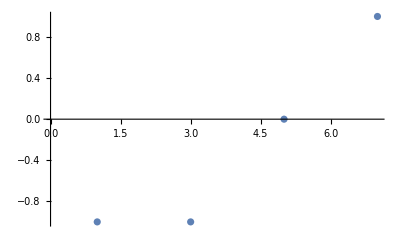

```mathematica
Dots={{0,0},{2,0},{5,0},{7,1}};
ListPlot[Dots]
```